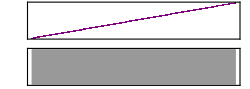

```mathematica
Sound[Table[SoundNote[k-48],{k,0,101}],30]
```

```mathematica
Export["C:\\Users\\User\\Desktop\\sounds\\spectrepiano.mid",Sound[Table[SoundNote[k-48],{k,0,101}],30]]
```

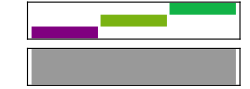

```mathematica
Sound[SoundNote[#,1,{"Piano","Cello","Tuba"}[[#]]]& /@ Range[3], 4]
```

```mathematica
Export["C:\\Users\\User\\Desktop\\sounds\\timbre.mid",Sound[SoundNote[#,1,{"Piano","Cello","Tuba"}[[#]]]& /@ Range[3], 4]]
```

C:\Users\User\Desktop\sounds\timbre.mid

```mathematica
Play[Piecewise[{{Sin[400 2Pi t],t<2},{Sin[404 2Pi t],t>2}}],{t,0,4}]
```

-Graphics-

```mathematica
Export["C:\\Users\\User\\Desktop\\sounds\\ensequence.wav",Play[Piecewise[{{Sin[400 2Pi t],t<2},{Sin[404 2Pi t],t>2}}],{t,0,4}]]
```

C:\Users\User\Desktop\sounds\ensequence.wav

```mathematica
Play[{Sin[400 2Pi t],Sin[404 2Pi t]},{t,0,2}]
```

-Graphics-

```mathematica
Export["C:\\Users\\User\\Desktop\\sounds\\battement.wav",Play[{Sin[400 2Pi t],Sin[404 2Pi t]},{t,0,2}]]
```

C:\Users\User\Desktop\sounds\battement.wav

```mathematica
auclairdelalune=Transpose[{{0,0,0,2,4,2,0,4,2,2,0}-6,{t,t,t,t,2t,2t,t,t,t,t,4t}}];
```

```mathematica
{#[[1]]+12,#[[2]]}&/@auclairdelalune
```

{{6,t},{6,t},{6,t},{8,t},{10,2 t},{8,2 t},{6,t},{10,t},{8,t},{8,t},{6,4 t}}

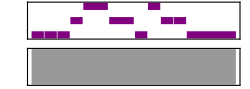

```mathematica
Sound[SoundNote@@@auclairdelalune]/.t->1/5
```

```mathematica
Export["C:\\Users\\User\\Desktop\\sounds\\spectre.wav",SoundNote@@@auclairdelalune/.t->1/5]
```

Export::nodta: {SoundNote[-6, 1/5], SoundNote[-6, 1/5], SoundNote[-6, 1/5], SoundNote[-4, 1/5], SoundNote[-2, 2/5], SoundNote[-4, 2/5], SoundNote[-6, 1/5], SoundNote[-2, 1/5], SoundNote[-4, 1/5], SoundNote[-4, 1/5], SoundNote[-6, 4/5]} contains no data that can be exported to the "WAV" format.

$Failed

```mathematica
Sound[SoundNote@@@({#[[1]]+12,#[[2]]}&/@auclairdelalune)]/.t->1/5
```

-Graphics-

```mathematica
Sound[SoundNote@@@({#[[1]]+7,#[[2]]}&/@auclairdelalune)]/.t->1/5
```

-Graphics-

```mathematica
Plot[Piecewise[{{Sin[400 2Pi t],x<2},{Sin[404 2Pi t],x>2}}],{x,-2,2}]
```

```mathematica
Export["C:\\Users\\User\\Desktop\\sounds\\ensequence.wav",Play[Piecewise[{{Sin[400 2Pi t],t<2},{Sin[404 2Pi t],t>2}}],{t,0,4}]]
```

C:\Users\User\Desktop\sounds\ensequence.wav

```mathematica
Play[{Sin[400 2Pi t],Sin[404 2Pi t]},{t,0,2}]
```

-Graphics-

```mathematica
Export["C:\\Users\\User\\Desktop\\sounds\\battement.wav",Play[{Sin[400 2Pi t],Sin[404 2Pi t]},{t,0,1}]]
```

C:\Users\User\Desktop\sounds\battement.wav

```mathematica
Export["battement.wav",Play[{Sin[400 2Pi t],Sin[404 2Pi t]},{t,0,1}]]
```

battement.wav

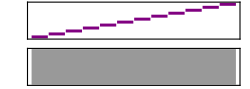

```mathematica
Sound[Table[SoundNote[k-6],{k,0,11}],3]
```

```mathematica
majeur={2,2,1,2,2,2,1};majeur=Prepend[Accumulate[majeur],0]
```

{0,2,4,5,7,9,11,12}

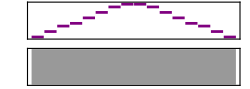

```mathematica
Sound[SoundNote/@(Join[majeur,Reverse[majeur]]-6),6]
```

```mathematica
mineurnat={2,1,2,2,1,2,2};mineurnat=Prepend[Accumulate[mineurnat],0]
```

{0,2,3,5,7,8,10,12}

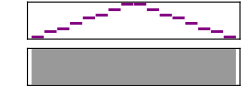

```mathematica
Sound[SoundNote/@(Join[mineurnat,Reverse[mineurnat]]-6),10]
```

```mathematica
mineurharm={2,1,2,2,1,3,1};mineurharm=Prepend[Accumulate[mineurharm],0]
```

{0,2,3,5,7,8,11,12}

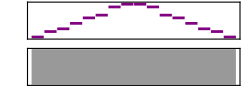

```mathematica
Sound[SoundNote/@(Join[mineurharm,Reverse[mineurharm]]-6),6]
```

```mathematica
mineurmelo={2,1,2,2,2,2,1};mineurmelo=Prepend[Accumulate[mineurmelo],0]
```

{0,2,3,5,7,9,11,12}

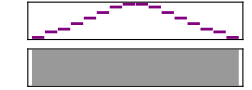

```mathematica
Sound[SoundNote/@(Join[mineurmelo,Reverse[mineurmelo]]-6),10]
```

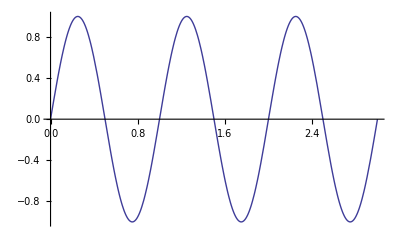

```mathematica
Plot[Sin[2π x],{x,0,3}]
```

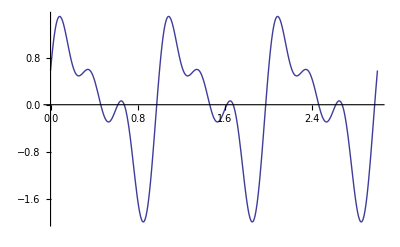

```mathematica
Plot[Sin[2π x]+1/2 Sin[2π  2x]+1/3 Sin[2π 3x+π/3]+1/4 Sin[2π  2x+π/4]+1/5 Sin[2π 3x+π/5],{x,0,3}]
```

```mathematica
Table[2^(k/12),{k,0,12}]//N
```

{1.,1.05946,1.12246,1.18921,1.25992,1.33484,1.41421,1.49831,1.5874,1.68179,1.7818,1.88775,2.}

```mathematica
Table[1.5^k,{k,0,12}]        (*12 quintes équivalent à 7 octaves*)
```

{1.,1.5,2.25,3.375,5.0625,7.59375,11.3906,17.0859,25.6289,38.4434,57.665,86.4976,129.746}

```mathematica
Table[Mod[7k,12],{k,-1,12}]
```

{5,0,7,2,9,4,11,6,1,8,3,10,5,0}

```mathematica
{5,0,7,2,9,4,11,6,1,8,3,10,5,0}       (*Cycle des quintes ascendantes : do re mi fa sol la si*)
```

```mathematica
Table[Mod[5k,12],{k,13,0,-1}]                     (*Cycle des quartes descendantes : do re mi fa sol la si*)
```

{5,0,7,2,9,4,11,6,1,8,3,10,5,0}

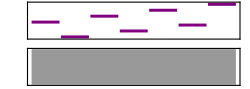

```mathematica
Sound[SoundNote/@{5,0,7,2,9,4,11},2]
```

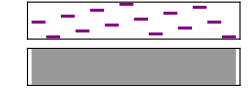

```mathematica
Sound[SoundNote/@{5,0,7,2,9,4,11,6,1,8,3,10,5,0},3]
```

```mathematica
Table[1.3333^k,{k,0,12}]          (*12 quartes équivalent à 6 octaves*)
```

{1.,1.3333,1.77769,2.37019,3.16018,4.21347,5.61781,7.49023,9.98672,13.3153,17.7533,23.6705,31.5598}

```mathematica
Rationalize[N[Table[2^(k/12),{k,12}]],0.02]
```

{17/16,9/8,6/5,5/4,4/3,7/5,3/2,8/5,5/3,9/5,15/8,2}

```mathematica
Rationalize[N[Table[2^(k/19),{k,19}]],0.02]
```

{27/26,14/13,9/8,7/6,6/5,5/4,9/7,4/3,7/5,10/7,3/2,14/9,8/5,5/3,12/7,9/5,13/7,21/11,2}

```mathematica
Rationalize[N[Table[2^(k/11),{k,18}]],0.02]
```

{16/15,8/7,6/5,9/7,11/8,13/9,11/7,5/3,7/4,15/8,2,15/7,9/4,12/5,18/7,11/4,29/10,28/9}

```mathematica
auclairdelalune=Transpose[{{0,0,0,2,4,2,0,4,2,2,0}-6,{t,t,t,t,2t,2t,t,t,t,t,4t}}];
```

```mathematica
Sound[SoundNote@@@auclairdelalune]/.t->1/5
```

-Graphics-

```mathematica
auclairdelalunerev=Transpose[{Reverse[{0,0,0,2,4,2,0,4,2,2,0}-6],Reverse[{t,t,t,t,2t,2t,t,t,t,t,4t}]}];
```

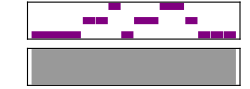

```mathematica
Sound[SoundNote@@@auclairdelalunerev]
```

```mathematica
auclairdelalunemir=Transpose[{-{0,0,0,2,4,2,0,4,2,2,0}+6,{t,t,t,t,2t,2t,t,t,t,t,4t}}];
```

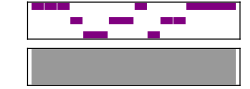

```mathematica
Sound[SoundNote@@@auclairdelalunemir]
```

```mathematica
auclairdelalunerevmir=Transpose[{Reverse[-{0,0,0,2,4,2,0,4,2,2,0}+6],Reverse[{t,t,t,t,2t,2t,t,t,t,t,4t}]}];
```

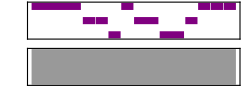

```mathematica
Sound[SoundNote@@@auclairdelalunerevmir]
```

```mathematica
Sound[SoundNote[auclairdelalune,auclairdelalunemir]]
```

Sound[SoundNote[{{-6,0.33},{-4,0.33},{-4,0.33},{-2,0.33},{-6,0.66},{-4,0.66},{-2,0.33},{-4,0.33},{-6,0.33},{-6,0.33},{-6,1.32}},{{6,0.33},{6,0.33},{6,0.33},{4,0.33},{2,0.66},{4,0.66},{6,0.33},{2,0.33},{4,0.33},{4,0.33},{6,1.32}}]]

```mathematica
auclairdelalune
```

{{-6,0.33},{-4,0.33},{-4,0.33},{-2,0.33},{-6,0.66},{-4,0.66},{-2,0.33},{-4,0.33},{-6,0.33},{-6,0.33},{-6,1.32}}

```mathematica
auclairdelalunemir
```

{{6,0.33},{6,0.33},{6,0.33},{4,0.33},{2,0.66},{4,0.66},{6,0.33},{2,0.33},{4,0.33},{4,0.33},{6,1.32}}

```mathematica
Transpose[auclairdelalune]
```

{{-6,-4,-4,-2,-6,-4,-2,-4,-6,-6,-6},{0.33,0.33,0.33,0.33,0.66,0.66,0.33,0.33,0.33,0.33,1.32}}